## Dark Energy Potential

October 29, 2020

#### Starobinsky Potential Approximation from Planck paper Table 5,

→ V(ϕ)=(1-e^-ϕ)^2

#### Yuan’s Dark Energy Potential w/ parameters,

→ V(ϕ)=7/(48(0.005))(e^(-2 ϕ/7.637626158259733)-2 e^(-ϕ/7.637626158259733)+1.1905508 e^((-2ϕ)/(3(7.637626158259733))))

h=1/(√2)
L=-h^2u''(ϕ)+V(ϕ)u(ϕ)
  =-h^2(d^2 u(ϕ))/dϕ^2+V(ϕ)u(ϕ)

#### where u(ϕ) is the wave function for the scalar field of the dark energy potential.

#### Yuan’s plots for her dark energy potential,

```mathematica
h=1/√2;V[x_]:=7/(48(.005)) (ⅇ^(-2x/7.637626158259733)-2 ⅇ^(-x/7.637626158259733)+1.1905508 ⅇ^(-2/3 x/7.637626158259733))
ℒ=-h^2*u''[x]+V[x]*u[x];{vals,funs}=NDEigensystem[ℒ,u[x],{x,-30,30},1,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

```mathematica
(* Note that NDEigensystem gives the n (1) smallest magnitude eigenvalues and eigenfunctions for the linear differential operator L over the region Omega (-30 30) *)
```

```mathematica
vals
```

{0.200339}

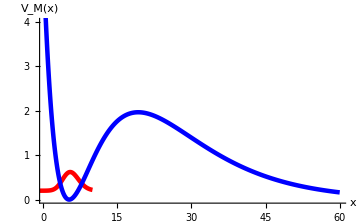

```mathematica
Show[Plot[Evaluate[h*funs+vals],{x,-10,10},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_M(x)"},PlotPoints->1000,  PlotStyle->{Red,Thickness[.009]}],Plot[V[x],{x,.5,60},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_(x)"},PlotPoints->1000,  PlotStyle->{Blue,Thickness[.009]}],PlotRange->{{.5,60},{0,4}},AxesOrigin->{-5,0},ImageSize->Medium]
```

#### Now I’m going to vary the value of the constant term out front,

```mathematica
Clear[L,V]
```

```mathematica
h=1/√2;
V[ϕ_]:=100(ⅇ^(-2ϕ/7.637626158259733)-2 ⅇ^(-ϕ/7.637626158259733)+1.1905508 ⅇ^(-2/3 ϕ/7.637626158259733))
ℒ=-h^2*u''[ϕ]+V[ϕ]*u[ϕ];{vals,funs}=NDEigensystem[ℒ,u[ϕ],{ϕ,-30,30},1,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

```mathematica
vals
```

{0.3742}

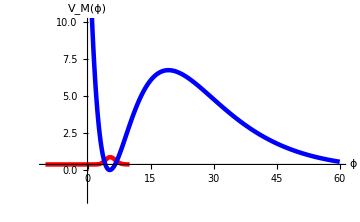

```mathematica
Show[Plot[Evaluate[h*funs+vals],{ϕ,-10,10},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"ϕ","V_M(ϕ)"},PlotPoints->1000,  PlotStyle->{Red,Thickness[.009]}],Plot[V[ϕ],{ϕ,.5,60},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"ϕ","V_(ϕ)"},PlotPoints->1000,  PlotStyle->{Blue,Thickness[.009]}],PlotRange->{{-10,60},{-2,10}},ImageSize->Medium]
```

#### Now I’m going to vary the 3rd term’s coefficient with the new constant out front,

```mathematica
Clear[L,V]
```

```mathematica
h=1/√2;
V[ϕ_]:=100(ⅇ^(-2ϕ/7.637626158259733)-2 ⅇ^(-ϕ/7.637626158259733)+1.1845575279846237 ⅇ^(-2/3 ϕ/7.637626158259733))
ℒ=-h^2*u''[ϕ]+V[ϕ]*u[ϕ];{vals,funs}=NDEigensystem[ℒ,u[ϕ],{ϕ,-30,30},1,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

```mathematica
vals
```

{1.11637×10^-6}

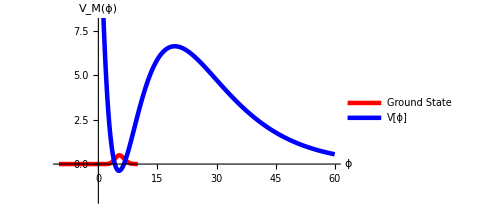

```mathematica
Show[Plot[Evaluate[h*funs+vals],{ϕ,-10,10},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"ϕ","V_M(ϕ)"},PlotPoints->1000,  PlotStyle->{Red,Thickness[.009]},PlotLegends->{"Ground State"}],Plot[V[ϕ],{ϕ,.5,60},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"ϕ","V_(ϕ)"},PlotPoints->1000,  PlotStyle->{Blue,Thickness[.009]},PlotLegends->{"V[ϕ]"}],PlotRange->{{-10,60},{-2,8}},ImageSize->Medium]
```

#### Now I’m going to vary the 3rd term’s coefficient slightly with a slider,

```mathematica
Clear[L,V]
```

```mathematica
h=1/√2;
V[x_,α_]:=100 (E^(-2 x/7.637626158259733)-2 E^(-x/7.637626158259733)+α*E^(-2/3 x/7.637626158259733))
L[α_]:=-h^2*u''[x]+V[x,α]*u[x]

f[α_]:=NDEigensystem[L[α],u[x],{x,-30,30},1,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}]

vals

Manipulate[{funs,vals}=f[α];
Show[Plot[h*funs+vals,{x,-10,10},AxesLabel->{"x","V(x)"},PlotStyle->Red,PlotPoints->1000],Plot[V[x,α],{x,0.5,60},PlotStyle->Blue,PlotPoints->1000],PlotRange->{{-20,60},{-5,10}}],{α,1,1.2}]
```

{InterpolatingFunction[…][x]}

Set::shape: Lists {funs,vals} and f[1.1965] are not the same shape.

#### Below is an animation of the same plot,

```mathematica
Animate[Show[Plot[h*funs+vals,{x,-10,10},AxesLabel->{"x","V(x)"},PlotStyle->Red,PlotPoints->1000],Plot[V[x,α],{x,0.5,60},PlotStyle->Blue,PlotPoints->1000],PlotRange->{{0,60},{-5,10}}],{α,1,1.2},AnimationRunning->False]
```

#### Let’s try to output the ground state energy using the matrix method with osc basis 16x16,

```mathematica
s=SparseArray[{{i_,i_}->0,{i_,j_}/;i-j==-1->√(j-1)},{16,16}]
```

SparseArray[…]

```mathematica
Xosc:=1/(√2)N[s+Transpose[s]]
```

```mathematica
Posc:= ⅈ/(√2)N[(-s+Transpose[s])]
```

```mathematica
Hdarkenergyosc:= .5Posc.Posc+100(MatrixExp[-2Xosc/7.637626158259733]- 2 MatrixExp[-Xosc/7.637626158259733] + 1.1845575279846237MatrixExp[-2/3 Xosc/7.637626158259733])
```

```mathematica
Reverse[N[Eigenvalues[Hdarkenergyosc]]]
```

{0.437916,2.0954,4.11158,6.48306,9.25646,12.5185,16.3977,21.0692,26.7629,33.7792,42.5208,53.552,67.7155,86.3892,112.173,151.589}

```mathematica
Hdarkenergyosc=Chop[Hdarkenergyosc];
SetDirectory[NotebookDirectory[]];
saveHam[ham_]:=Export["./"<>"Hdarkenergyosc16x16.txt",ham,"Table"]

saveHam[Hdarkenergyosc];
```

#### Same thing but with 32x32,

```mathematica
s=SparseArray[{{i_,i_}->0,{i_,j_}/;i-j==-1->√(j-1)},{32,32}]
```

SparseArray[…]

```mathematica
Xosc:=1/(√2)N[s+Transpose[s]]
```

```mathematica
Posc:= ⅈ/(√2)N[(-s+Transpose[s])]
```

```mathematica
Hdarkenergyosc:= .5Posc.Posc+100(MatrixExp[-2Xosc/7.637626158259733]- 2 MatrixExp[-Xosc/7.637626158259733] + 1.1845575279846237MatrixExp[-2/3 Xosc/7.637626158259733])
```

```mathematica
Reverse[N[Eigenvalues[Hdarkenergyosc]]]
```

{0.00285585,0.779618,1.65619,2.69198,3.88797,5.2333,6.7217,8.35224,10.1287,12.0595,14.1586,16.4469,18.955,21.7269,24.8229,28.3216,32.3197,36.9301,42.2814,48.5203,55.817,64.3735,74.4364,86.3132,100.397,117.206,137.443,162.103,192.688,231.653,283.649,360.363}

```mathematica
Hdarkenergyosc=Chop[Hdarkenergyosc];
SetDirectory[NotebookDirectory[]];
saveHam[ham_]:=Export["./"<>"Hdarkenergyosc32x32.txt",ham,"Table"]

saveHam[Hdarkenergyosc];
```

#### Same thing but with 64x64,

```mathematica
s=SparseArray[{{i_,i_}->0,{i_,j_}/;i-j==-1->√(j-1)},{64,64}]
```

SparseArray[…]

```mathematica
Xosc:=1/(√2)N[s+Transpose[s]]
```

```mathematica
Posc:= ⅈ/(√2)N[(-s+Transpose[s])]
```

```mathematica
Hdarkenergyosc:= .5Posc.Posc+100(MatrixExp[-2Xosc/7.637626158259733]- 2 MatrixExp[-Xosc/7.637626158259733] + 1.1845575279846237MatrixExp[-2/3 Xosc/7.637626158259733])
```

```mathematica
Reverse[N[Eigenvalues[Hdarkenergyosc]]]
```

{1.11711×10^-6,0.736569,1.4446,2.1235,2.77539,3.41796,4.09462,4.84283,5.67157,6.57701,7.55423,8.5995,9.71026,10.8848,12.1221,13.4215,14.783,16.2069,17.6939,19.245,20.8617,22.5459,24.3001,26.127,28.0304,30.0146,32.085,34.2484,36.5131,38.8901,41.3933,44.0418,46.8616,49.8893,53.1741,56.7785,60.7742,65.2372,70.2433,75.8679,82.1872,89.2811,97.2366,106.15,116.132,127.306,139.816,153.827,169.534,187.163,206.981,229.305,254.519,283.086,315.58,352.719,395.42,444.888,502.753,571.321,654.048,756.597,889.665,1080.19}

```mathematica
Hdarkenergyosc=Chop[Hdarkenergyosc];
SetDirectory[NotebookDirectory[]];
saveHam[ham_]:=Export["./"<>"Hdarkenergyosc64x64.txt",ham,"Table"]

saveHam[Hdarkenergyosc];
```